```mathematica
kernel[t_,x_]=(1+Abs[x-t])Exp[-Abs[x-t]]
```

ⅇ^(-Abs[-t+x]) (1+Abs[-t+x])

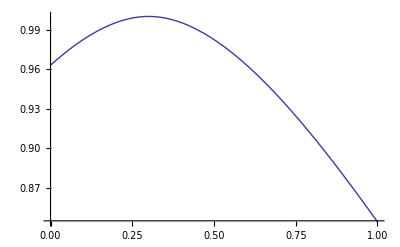

```mathematica
Plot[kernel[t,0.3],{t,0,1},PlotStyle ->Thick]
```

```mathematica
dtkernel[t_,x_]=-(t-x)Exp[-Abs[x-t]]
```

ⅇ^(-Abs[-t+x]) (-t+x)

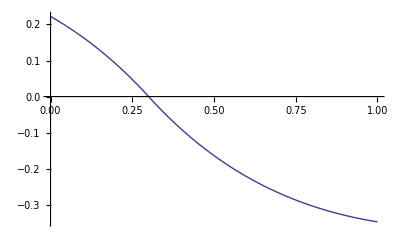

```mathematica
Plot[dtkernel[t,0.3],{t,0,1},PlotStyle ->Thick]
```

```mathematica
dtxkernel[x_,t_]=Exp[-Abs[x-t]](1-Abs[x-t])
```

ⅇ^(-Abs[-t+x]) (1-Abs[-t+x])

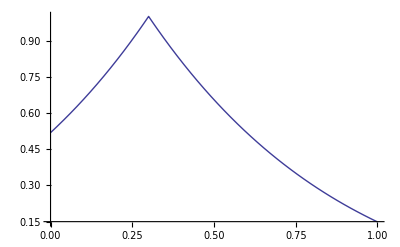

```mathematica
Plot[dtxkernel[t,0.3],{t,0,1},PlotStyle ->Thick]
```

```mathematica
a=Integrate [dtxkernel[t_,t_],{t,0,1}]
```

1

```mathematica
n=40
```

40

```mathematica
xpoints=Table[i/(n-1),{i,0,n-1}];
```

```mathematica
Kmatrix=Table[kernel[xpoints[[i]],xpoints[[j]]],{i,1,n},{j,1,n}];
```

```mathematica
kfun[x_]=Table[kernel[x,xpoints[[i]]],{i,1,n}];
```

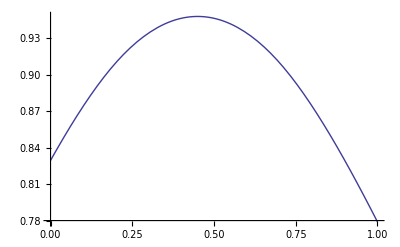

```mathematica
Plot [kernel[0.2,x]*kernel[0.7,x],{x,0,1}]
```

```mathematica
Integrate [kernel[0.2,x]*kernel[0.7,x],{x,0,0.2}]+Integrate [kernel[0.2,x]*kernel[0.7,x],{x,0.2,0.7}]+Integrate [kernel[0.2,x]*kernel[0.7,x],{x,0.7,1}]
```

0.897

```mathematica
Assuming[0<t <s<1,Integrate [kernel[t,x]*kernel[s,x],{x,0,1}]]
```

-1/12 ⅇ^(-2-s) (-15 ⅇ^(2+t)+39 ⅇ^(2 s+t)-21 ⅇ^(2+t) s-15 ⅇ^(2 s+t) s-12 ⅇ^(2+t) s^2-2 ⅇ^(2+t) s^3+21 ⅇ^(2+t) t-15 ⅇ^(2 s+t) t+24 ⅇ^(2+t) s t+6 ⅇ^(2 s+t) s t+6 ⅇ^(2+t) s^2 t-12 ⅇ^(2+t) t^2-6 ⅇ^(2+t) s t^2+2 ⅇ^(2+t) t^3+18 ⅇ^2 t Cosh[t]+6 ⅇ^2 s t Cosh[t]-30 ⅇ^2 Sinh[t]-18 ⅇ^2 s Sinh[t]-6 ⅇ^2 s t Sinh[t])

```mathematica
xuan[t_,s_]=ExpandAll[-1/12 ⅇ^(-2-s) (-15 ⅇ^(2+t)+39 ⅇ^(2 s+t)-21 ⅇ^(2+t) s-15 ⅇ^(2 s+t) s-12 ⅇ^(2+t) s^2-2 ⅇ^(2+t) s^3+21 ⅇ^(2+t) t-15 ⅇ^(2 s+t) t+24 ⅇ^(2+t) s t+6 ⅇ^(2 s+t) s t+6 ⅇ^(2+t) s^2 t-12 ⅇ^(2+t) t^2-6 ⅇ^(2+t) s t^2+2 ⅇ^(2+t) t^3+18 ⅇ^2 t Cosh[t]+6 ⅇ^2 s t Cosh[t]-30 ⅇ^2 Sinh[t]-18 ⅇ^2 s Sinh[t]-6 ⅇ^2 s t Sinh[t])]
```

(5 ⅇ^(-s+t))/4-13/4 ⅇ^(-2+s+t)+7/4 ⅇ^(-s+t) s+5/4 ⅇ^(-2+s+t) s+ⅇ^(-s+t) s^2+1/6 ⅇ^(-s+t) s^3-7/4 ⅇ^(-s+t) t+5/4 ⅇ^(-2+s+t) t-2 ⅇ^(-s+t) s t-1/2 ⅇ^(-2+s+t) s t-1/2 ⅇ^(-s+t) s^2 t+ⅇ^(-s+t) t^2+1/2 ⅇ^(-s+t) s t^2-1/6 ⅇ^(-s+t) t^3-3/2 ⅇ^-s t Cosh[t]-1/2 ⅇ^-s s t Cosh[t]+5/2 ⅇ^-s Sinh[t]+3/2 ⅇ^-s s Sinh[t]+1/2 ⅇ^-s s t Sinh[t]

```mathematica
xuan[0.2,0.7]
```

0.897

```mathematica
Integrate[kernel[t,x]*kernel[s,x],{x,0,1}]
```

$Aborted

```mathematica
fred=Inverse[N[Kmatrix]];
```

```mathematica
piece[x_]=kfun[x].fred.kfun[x];
```

```mathematica
b=Integrate[piece[x],{x,0,1}]
```

$Aborted

```mathematica
a-b
```

0.000973306